```mathematica
Fsol =NDSolve[{F'''[ζ] + 1/2 F[ζ]F''[ζ]==0,F[0]== 0,F'[0]== 0,F''[0]==1},F[ζ],{ζ,0,10000}];
```

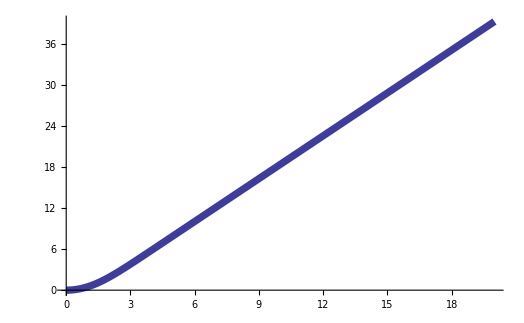

```mathematica
Plot[F[ζ] /. Fsol,{ζ,0,20},PlotStyle -> Thickness[0.01], LabelStyle->Large]
```

```mathematica
CC = D[F[ζ]/. Fsol[[1]],{ζ,1}]/. ζ -> 20
```

2.08541

```mathematica
α = 1/CC^(1/2)
```

0.692475

```mathematica
f[η_]:=α F[ζ]/. Fsol[[1]] /. ζ -> α η
```

```mathematica
α1=f''[0]
```

0.332057

```mathematica
β1 = 20 -f[20]
```

1.72079

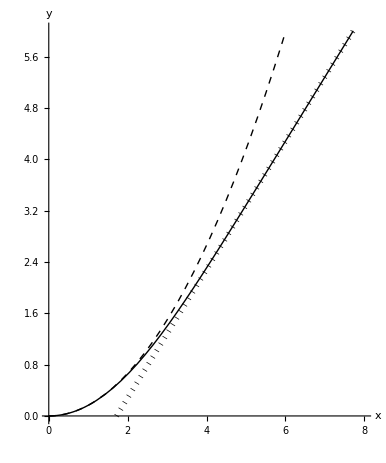

```mathematica
p =Plot[{f[η],0.5 f''[0] η^2,η-(20-f[20])},{η,0,10},PlotStyle -> {{Thick,Black},{Thick,Dashed,Black},{Thickness[0.01],Dotted,Black}},PlotRange -> {{0,8},{0,6}},AspectRatio ->1.2,LabelStyle -> 20,AxesLabel-> {x,y}]
```

```mathematica
Export["/Users/jbfreund/jbfreund/T/blasius-asm.eps",p,"EPS"];
```

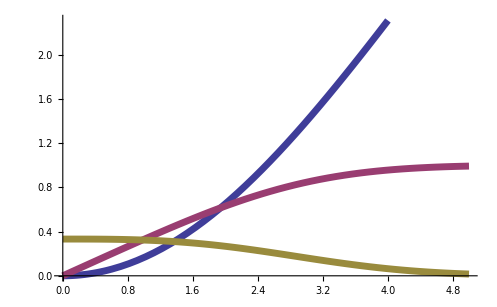

```mathematica
Plot[{f[η],f'[η],f''[η]},{η,0,5},PlotStyle -> Thickness[0.01], LabelStyle->Large]
```

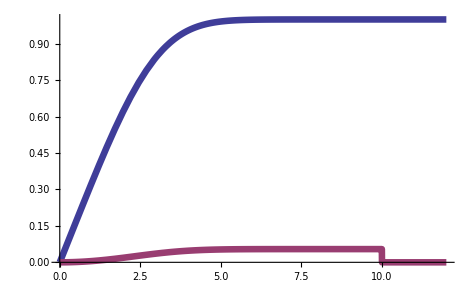

```mathematica
Plot[{f'[η],If[η<10,√(10^-2 1/10)(η f'[η]-f[η]),0]},{η,0,12},PlotStyle -> Thickness[0.01], LabelStyle->Large]
```

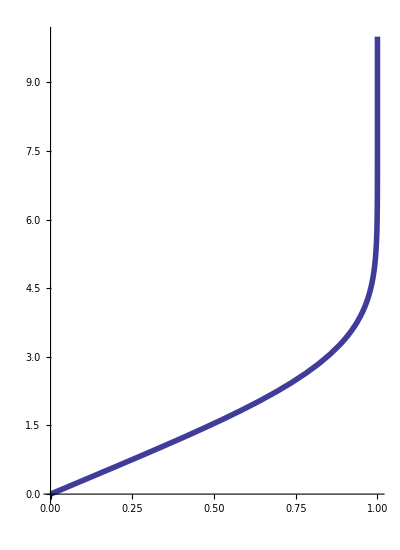

```mathematica
bplt=ParametricPlot[{f'[η],η},{η,0,10},AspectRatio -> GoldenRatio*0.85,PlotStyle ->Thickness[0.01]]
```

```mathematica
bplt=ParametricPlot[{f'[η],η},{η,0,10},AspectRatio -> GoldenRatio*0.85,PlotStyle -> {White,Thickness[0.01]},Background ->  Black];
```

```mathematica
bim = -Graphics-;
```

```mathematica
ImageRotate[bim,1.3π/180]
```

-Graphics-

```mathematica
ImageAdd[ImageRotate[bim,1.3π/180],Show[bplt,PlotRange -> {{0,1.08},{-.3,7.3}}]]
```

-Graphics-

```mathematica
(* composite solution *)
ψc[x_,y_,R_]:= (√x)/R^(1/2)f[(y R^(1/2))/(√x)]-β1/R^(1/2)√(x + ⅈ y)+β1/R^(1/2)√x
```

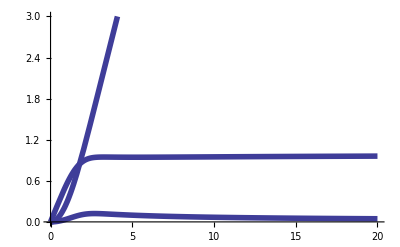

```mathematica
Plot[{Re[ψc[x,y,10]],Re[D[ψc[x,ξ,10],ξ]] /. ξ -> y,-Re[D[ψc[ξ,y,10],ξ]] /. ξ -> x} /. x -> 3,{y,0,20},PlotRange -> {All,{0,3}},PlotStyle -> Thickness[0.01], LabelStyle->Large]
```

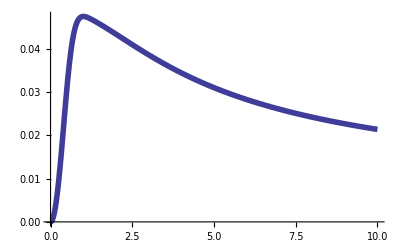

```mathematica
(* v velocity *)
Plot[{-Re[D[ψc[ξ,y,100],ξ]] /. ξ -> x} /. x -> 3,{y,0,10},PlotRange -> All,PlotStyle -> Thickness[0.01], LabelStyle->Large]
```

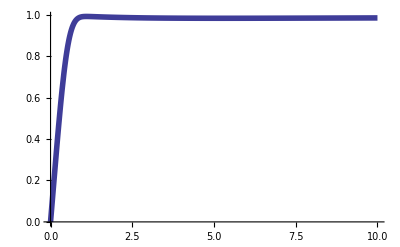

```mathematica
(* u velocity *)
Plot[{Re[D[ψc[x,ξ,100],ξ]] /. ξ -> y}/. x -> 3,{y,0,10},PlotRange -> All,PlotStyle -> Thickness[0.01], LabelStyle->Large]
```

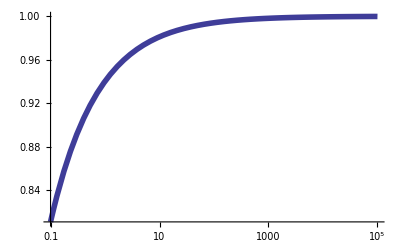

```mathematica
LogLinearPlot[{Re[D[ψc[3,ξ,R],ξ]] /. ξ -> 100},{R,.1,10^5},PlotRange -> All,PlotStyle -> Thickness[0.01], LabelStyle->Large]
```